```mathematica
(*DumpSave["Shape Basis 2.mx",{a,F}];*)
```

```mathematica
Get["Shape Basis 2.mx"]
```

## Shape basis 2

```mathematica
Subscript[θ, 1,1][1]=0;Subscript[θ, 1,2][1]=0;Subscript[θ, 1,3][1]=0;Subscript[θ, 1,4][1]=0;Subscript[θ, 2,1][1]=0;Subscript[θ, 2,2][1]=0;Subscript[θ, 2,3][1]=0;
```

```mathematica
steps=100;
dtheta= Pi/(steps-1);
```

```mathematica
Clear[ω]
```

```mathematica
Clear[w1,w2,u];
alpha[u_,w1_,w2_]=w1 Sin[ω u]+w2 Cos[ω u];
```

```mathematica
R={ {Sin[4 ω],Cos[4ω ]} , {Sin[5ω ],Cos[5 ω]}, {Sin[6 ω],Cos[6 ω]},      {Sin[7 ω],Cos[7 ω]}        ,        {-Sin[3ω],-Cos[3ω]}          ,          {-Sin[2 ω],-Cos[2 ω]}         ,       {-Sin[ω],-Cos[ω]} };(*jacobian of the 7 dimensional input wrt the 2 dimensional input*)
```

```mathematica
R//TableForm
```

Sin[4 ω] | Cos[4 ω]
Sin[5 ω] | Cos[5 ω]
Sin[6 ω] | Cos[6 ω]
Sin[7 ω] | Cos[7 ω]
-Sin[3 ω] | -Cos[3 ω]
-Sin[2 ω] | -Cos[2 ω]
-Sin[ω] | -Cos[ω]

```mathematica
Clear[a,q1,q2]
```

```mathematica
For[p=2,p≤16,p++,ω=Pi/p;For[i=1,i≤steps,i++,ww1=-Pi/2+(i-1) dtheta;For[j=1,j≤steps,j++,ww2=-Pi/2+(j-1) dtheta;q1=x1/.{Subscript[θ, 1,1][t]-> alpha[4,ww1,ww2],Subscript[θ, 1,2][t]-> alpha[5,ww1,ww2],Subscript[θ, 1,3][t]-> alpha[6,ww1,ww2],Subscript[θ, 1,4][t]-> alpha[7,ww1,ww2],Subscript[θ, 2,1][t]-> -alpha[3,ww1,ww2],Subscript[θ, 2,2][t]-> -alpha[2,ww1,ww2],Subscript[θ, 2,3][t]-> -alpha[1,ww1,ww2]};q2=y1/.{Subscript[θ, 1,1][t]-> alpha[4,ww1,ww2],Subscript[θ, 1,2][t]-> alpha[5,ww1,ww2],Subscript[θ, 1,3][t]-> alpha[6,ww1,ww2],Subscript[θ, 1,4][t]-> alpha[7,ww1,ww2],Subscript[θ, 2,1][t]-> -alpha[3,ww1,ww2],Subscript[θ, 2,2][t]-> -alpha[2,ww1,ww2],Subscript[θ, 2,3][t]-> -alpha[1,ww1,ww2]};a[i,j,p]=Chop[(Inverse[q1].q2)[[4;;6]].R]]]]
```

$Aborted

```mathematica
adata=Table[a[i,j,1],{i,1,steps},{j,1,steps}];
```

```mathematica
adata//TableForm;
```

### Finding the height functions

```mathematica
For[p=2,p≤16,p++,For[i=1,i≤steps-1,i++,For[j=1,j≤steps-1,j++,For[k=1,k≤3,k++,Subscript[df, 1]=(a[i,j+1,p][[k,1]]-a[i,j,p][[k,1]])/dtheta;Subscript[df, 2]=(a[i+1,j,p][[k,2]]-a[i,j,p][[k,2]])/dtheta;F[i,j,k,p]=Subscript[df, 2]-Subscript[df, 1]]]]];
```

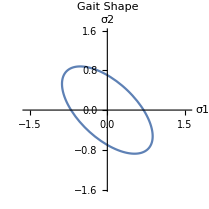

```mathematica
Show[ParametricPlot[{π/8 (2Sin[t]+Cos[ t]) , π/8 (-2Sin[t]+Cos[ t])},{t,0,2Pi}],AxesLabel->{HoldForm[σ1],HoldForm[σ2]},PlotLabel->HoldForm[Gait Shape],LabelStyle->{GrayLevel[0]},PlotRange->{{-Pi/2,Pi/2},{-Pi/2,Pi/2}}]
```

```mathematica
zeros=ConstantArray[0,{steps-1,steps-1}];
```

```mathematica
Clear[plot]
```

```mathematica
For[p=2,p≤16,p++,For[k=1,k≤3,k++,F1data=Table[F[i,j,k,p],{i,1,steps-1},{j,1,steps-1}];
plot[p,k]=Show[{ListPlot3D[F1data,ColorFunction->"Rainbow"],ListPlot3D[zeros]}];]]
```

```mathematica
Table[plot[p,k],{p,2,16,1},{k,1,3,1}]//TableForm
```

-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-

## Numerical Simulation (USING SHAPE BASIS)

### Around X axis

```mathematica
timeStep=100;
duration=2 Pi;
dt=duration/timeStep;

Clear[α,β,γ]
```

initialization

```mathematica
e=0;
```

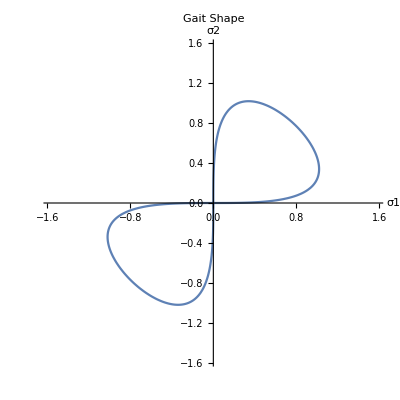

```mathematica
gait[t_]={w1->π/8 (2Sin[t]+Sin[2t])  ,w2->π/8 (2Sin[t]-Sin[2 t])};
ω=Pi/3;
Clear[w1,w2,u];
alpha[u_,w1_,w2_]=w1 Sin[ω u]+w2 Cos[ω u];
R={ {Sin[4 ω],Cos[4ω ]} , {Sin[5ω ],Cos[5 ω]}, {Sin[6 ω],Cos[6 ω]},      {Sin[7 ω],Cos[7 ω]}        ,        {-Sin[3ω],-Cos[3ω]}          ,          {-Sin[2 ω],-Cos[2 ω]}         ,       {-Sin[ ω],-Cos[ω]} };(*jacobian of the 7 dimensional input alpha wrt the 2 dimensional input {w1,w2}*)
R//TableForm;
Show[ParametricPlot[{w1/.gait[t],w2/.gait[t]},{t,0,2Pi}],AxesLabel->{HoldForm[σ1],HoldForm[σ2]},PlotLabel->HoldForm[Gait Shape],LabelStyle->{GrayLevel[0]},PlotRange->{{-Pi/2,Pi/2},{-Pi/2,Pi/2}}]
```

```mathematica
Table[plot[3,i],{i,1,3}]//TableForm
```

plot[3,1]
plot[3,2]
plot[3,3]

```mathematica
α[1]=0;β[1]=0;γ[1]=0;
Subscript[θ, 1,1][1]=alpha[4,w1,w2]/.gait[t]/.t-> 0;Subscript[θ, 1,2][1]=alpha[5,w1,w2]/.gait[t]/.t-> 0;Subscript[θ, 1,3][1]=alpha[6,w1,w2]/.gait[t]/.t-> 0;Subscript[θ, 1,4][1]=alpha[7,w1,w2]/.gait[t]/.t-> 0;Subscript[θ, 2,1][1]=-alpha[3,w1,w2]/.gait[t]/.t-> 0;Subscript[θ, 2,2][1]=-alpha[2,w1,w2]/.gait[t]/.t-> 0;Subscript[θ, 2,3][1]=-alpha[1,w1,w2]/.gait[t]/.t-> 0;
```

```mathematica
TL[t]={{1,0 , -Sin[β[t]]},{0,Cos[α[t]],Cos[β[t]] Sin[α[t]]},{0 ,-Sin[α[t]] , Cos[α[t]] Cos[β[t]] }};(*lifted Action on fiber tangent space as in Shammas, Choset,  Rizzi*)
TLinverse[t_]=Inverse[TL[t]];
Inverse[TL[t]]//TableForm;
```

```mathematica
rdot[t_]= R.{D[(w1/.gait[t]), t],D[(w2/.gait[t]), t]};(*base variables velocities {RightJoint 1,RightJoint 2,...,RightJoint n,LeftJoint 1,LeftJoint 2...LefttJoint m}*)
```

```mathematica
Clear[i];(*gdot is the velocity of the desired link in inertial frame coordinates, i.e {α',β',γ'}*)
For[i=1,i≤timeStep,i++,time=i dt;bodyVelocity=-(Inverse[x[i]].y[i])[[4;;6]].rdot[time];gdot=TLinverse[i].bodyVelocity;{{α[i+1],β[i+1],γ[i+1]}}=Transpose[dt gdot+{{α[i]},{β[i]},{γ[i]}}]; For[j=1,j≤nright,j++,Subscript[θ, 1,j][i+1]=N[alpha[nleft+j,w1,w2]]/.gait[time];];For[j=1,j≤nleft,j++,Subscript[θ, 2,j][i+1]=N[-alpha[nleft+1-j,w1,w2]]/.gait[time];]]
```

```mathematica
Table[{Subscript[θ, 1,1][t],Subscript[θ, 1,2][t],α[t],β[t],γ[t]},{t,1,timeStep+1}]//TableForm;
```

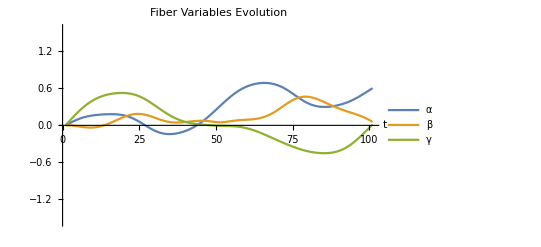

```mathematica
Show[ListLinePlot[{Table[α[t],{t,1,timeStep+1}],Table[β[t],{t,1,timeStep+1}],Table[γ[t],{t,1,timeStep+1}]},AxesLabel->{HoldForm[t],None},PlotLabel->HoldForm[Fiber Variables Evolution],LabelStyle->{GrayLevel[0],Bold},PlotLegends->{α,β,γ}],PlotRange->{-π/2,π/2}]
```

### Around Y axis

```mathematica
timeStep=100;
duration=2 Pi;
dt=duration/timeStep;
Clear[α,β,γ]
```

initialization

```mathematica
e=0;
```

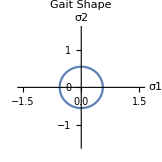

```mathematica
gait[t_]={w1->π/8 (Sin[t]+Cos[ t])  ,w2->π/8 (Sin[t]-Cos[ t])};
ω=Pi/16;
Clear[w1,w2,u];
alpha[u_,w1_,w2_]=w1 Sin[ω u]+w2 Cos[ω u];
R={ {Sin[4 ω],Cos[4ω ]} , {Sin[5ω ],Cos[5 ω]}, {Sin[6 ω],Cos[6 ω]},      {Sin[7 ω],Cos[7 ω]}        ,        {-Sin[3ω],-Cos[3ω]}          ,          {-Sin[2 ω],-Cos[2 ω]}         ,       {-Sin[ ω],-Cos[ω]} };(*jacobian of the 7 dimensional input alpha wrt the 2 dimensional input {w1,w2}*)
R//TableForm;
Show[ParametricPlot[{w1/.gait[t],w2/.gait[t]},{t,0,2Pi}],AxesLabel->{HoldForm[σ1],HoldForm[σ2]},PlotLabel->HoldForm[Gait Shape],LabelStyle->{GrayLevel[0]},PlotRange->{{-Pi/2,Pi/2},{-Pi/2,Pi/2}}]
```

```mathematica
α[1]=0;β[1]=0;γ[1]=0;
Subscript[θ, 1,1][1]=alpha[4,w1,w2]/.gait[t]/.t-> 0;Subscript[θ, 1,2][1]=alpha[5,w1,w2]/.gait[t]/.t-> 0;Subscript[θ, 1,3][1]=alpha[6,w1,w2]/.gait[t]/.t-> 0;Subscript[θ, 1,4][1]=alpha[7,w1,w2]/.gait[t]/.t-> 0;Subscript[θ, 2,1][1]=-alpha[3,w1,w2]/.gait[t]/.t-> 0;Subscript[θ, 2,2][1]=-alpha[2,w1,w2]/.gait[t]/.t-> 0;Subscript[θ, 2,3][1]=-alpha[1,w1,w2]/.gait[t]/.t-> 0;
```

```mathematica
TL[t]={{1,0 , -Sin[β[t]]},{0,Cos[α[t]],Cos[β[t]] Sin[α[t]]},{0 ,-Sin[α[t]] , Cos[α[t]] Cos[β[t]] }};(*lifted Action on fiber tangent space as in Shammas, Choset,  Rizzi*)
TLinverse[t_]=Inverse[TL[t]];
Inverse[TL[t]]//TableForm;
```

```mathematica
rdot[t_]= R.{D[(w1/.gait[t]), t],D[(w2/.gait[t]), t]};(*base variables velocities {RightJoint 1,RightJoint 2,...,RightJoint n,LeftJoint 1,LeftJoint 2...LefttJoint m}*)
```

```mathematica
Clear[i];(*gdot is the velocity of the desired link in inertial frame coordinates, i.e {α',β',γ'}*)
For[i=1,i≤timeStep,i++,time=i dt;bodyVelocity=-(Inverse[x[i]].y[i])[[4;;6]].rdot[time];gdot=TLinverse[i].bodyVelocity;{{α[i+1],β[i+1],γ[i+1]}}=Transpose[dt gdot+{{α[i]},{β[i]},{γ[i]}}]; For[j=1,j≤nright,j++,Subscript[θ, 1,j][i+1]=N[alpha[nleft+j,w1,w2]]/.gait[time];];For[j=1,j≤nleft,j++,Subscript[θ, 2,j][i+1]=N[-alpha[nleft+1-j,w1,w2]]/.gait[time];]]
```

```mathematica
Table[{Subscript[θ, 1,1][t],Subscript[θ, 1,2][t],α[t],β[t],γ[t]},{t,1,timeStep+1}]//TableForm;
```

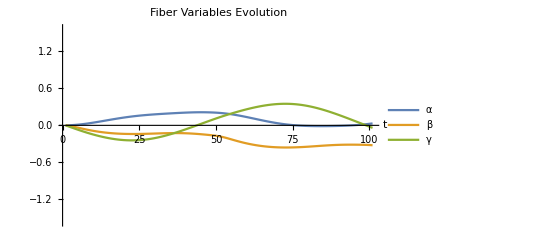

```mathematica
Show[ListLinePlot[{Table[α[t],{t,1,timeStep+1}],Table[β[t],{t,1,timeStep+1}],Table[γ[t],{t,1,timeStep+1}]},AxesLabel->{HoldForm[t],None},PlotLabel->HoldForm[Fiber Variables Evolution],LabelStyle->{GrayLevel[0],Bold},PlotLegends->{α,β,γ}],PlotRange->{-π/2,π/2}]
```

### Around Z axis

```mathematica
timeStep=100;
duration=2 Pi;
dt=duration/timeStep;
Clear[α,β,γ]
```

initialization

```mathematica
e=-0;
```

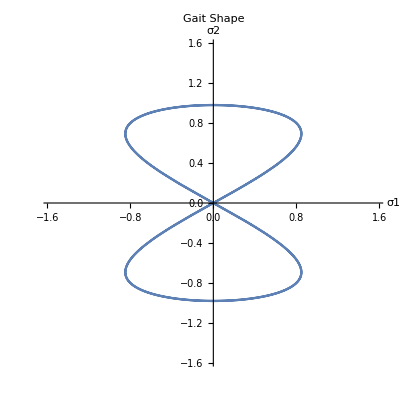

```mathematica
gait[t_]={w1->π/3.7 (Sin[4t])  ,w2->π/3.2 (Sin[2 t])};
ω=Pi/2.63;
Clear[w1,w2,u];
alpha[u_,w1_,w2_]=w1 Sin[ω u]+w2 Cos[ω u];
R={ {Sin[4 ω],Cos[4ω ]} , {Sin[5ω ],Cos[5 ω]}, {Sin[6 ω],Cos[6 ω]},      {Sin[7 ω],Cos[7 ω]}        ,        {-Sin[3ω],-Cos[3ω]}          ,          {-Sin[2 ω],-Cos[2 ω]}         ,       {-Sin[ ω],-Cos[ω]} };(*jacobian of the 7 dimensional input alpha wrt the 2 dimensional input {w1,w2}*)
R//TableForm;
Show[ParametricPlot[{w1/.gait[t],w2/.gait[t]},{t,0,2Pi}],AxesLabel->{HoldForm[σ1],HoldForm[σ2]},PlotLabel->HoldForm[Gait Shape],LabelStyle->{GrayLevel[0]},PlotRange->{{-Pi/2,Pi/2},{-Pi/2,Pi/2}}]
```

```mathematica
α[1]=0;β[1]=0;γ[1]=0;
Subscript[θ, 1,1][1]=alpha[4,w1,w2]/.gait[t]/.t-> 0;Subscript[θ, 1,2][1]=alpha[5,w1,w2]/.gait[t]/.t-> 0;Subscript[θ, 1,3][1]=alpha[6,w1,w2]/.gait[t]/.t-> 0;Subscript[θ, 1,4][1]=alpha[7,w1,w2]/.gait[t]/.t-> 0;Subscript[θ, 2,1][1]=-alpha[3,w1,w2]/.gait[t]/.t-> 0;Subscript[θ, 2,2][1]=-alpha[2,w1,w2]/.gait[t]/.t-> 0;Subscript[θ, 2,3][1]=-alpha[1,w1,w2]/.gait[t]/.t-> 0;
```

```mathematica
TL[t]={{1,0 , -Sin[β[t]]},{0,Cos[α[t]],Cos[β[t]] Sin[α[t]]},{0 ,-Sin[α[t]] , Cos[α[t]] Cos[β[t]] }};(*lifted Action on fiber tangent space as in Shammas, Choset,  Rizzi*)
TLinverse[t_]=Inverse[TL[t]];
Inverse[TL[t]]//TableForm;
```

```mathematica
rdot[t_]= R.{D[(w1/.gait[t]), t],D[(w2/.gait[t]), t]};(*base variables velocities {RightJoint 1,RightJoint 2,...,RightJoint n,LeftJoint 1,LeftJoint 2...LefttJoint m}*)
```

```mathematica
Clear[i];(*gdot is the velocity of the desired link in inertial frame coordinates, i.e {α',β',γ'}*)
For[i=1,i≤timeStep,i++,time=i dt;bodyVelocity=-(Inverse[x[i]].y[i])[[4;;6]].rdot[time];gdot=TLinverse[i].bodyVelocity;{{α[i+1],β[i+1],γ[i+1]}}=Transpose[dt gdot+{{α[i]},{β[i]},{γ[i]}}]; For[j=1,j≤nright,j++,Subscript[θ, 1,j][i+1]=N[alpha[nleft+j,w1,w2]]/.gait[time];];For[j=1,j≤nleft,j++,Subscript[θ, 2,j][i+1]=N[-alpha[nleft+1-j,w1,w2]]/.gait[time];]]
```

```mathematica
Table[{Subscript[θ, 1,1][t],Subscript[θ, 1,2][t],α[t],β[t],γ[t]},{t,1,timeStep+1}]//TableForm;
```

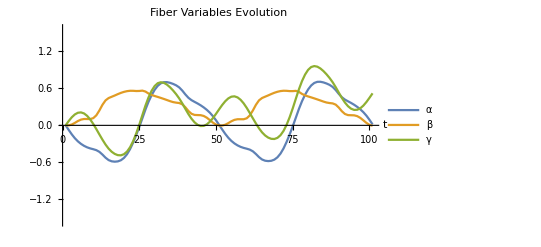

```mathematica
Show[ListLinePlot[{Table[α[t],{t,1,timeStep+1}],Table[β[t],{t,1,timeStep+1}],Table[γ[t],{t,1,timeStep+1}]},AxesLabel->{HoldForm[t],None},PlotLabel->HoldForm[Fiber Variables Evolution],LabelStyle->{GrayLevel[0],Bold},PlotLegends->{α,β,γ}],PlotRange->{-π/2,π/2}]
```